Area of lens = 12.0095

Area of Moon = 12.5664

Percent Illuminated = 4.4312

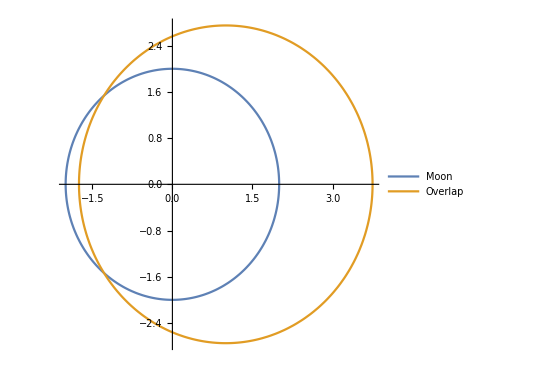

```mathematica
(* Anthony Torres
Created: 10/27/16
Calculates the percent of area "illuminated" after overlapping a black circle
Equation pulled from: http://mathworld.wolfram.com/Circle-CircleIntersection.html
*)
ClearAll["Global`*"]
r = 2.75; (* Overlap circle *)
R = 2; (* Moon circle *)
d = 1;
Alens = r^2*ArcCos[(d^2+r^2-R^2)/(2*d*r)]+R^2*ArcCos[(d^2+R^2-r^2)/(2*d*R)]-1/2*Sqrt[(-d+r+R)(d+r-R)(d-r+R)(d+r+R)];
Amoon = N[π*R^2];
PerIllum = N[(Amoon-Alens)/Amoon*100];
Print["Area of lens = ",Alens]
Print["Area of Moon = ", Amoon]
Print["Percent Illuminated = ",PerIllum]
ParametricPlot[{{R*Cos[u],R*Sin[u]},{d+ r*Cos[u],r*Sin[u]}},{u,0,2π},PlotLegends->{"Moon","Overlap"}]
```